## VoronoiToTissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 19:16:42
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
r:= RandomReal[{0, 100}]; 
xy:= {r, r}; 
v=Table[xy, {25}];
p={{-2, -2.5}, {110, -1}, {105, 107},{73, 119},  {-3, 106}};
```

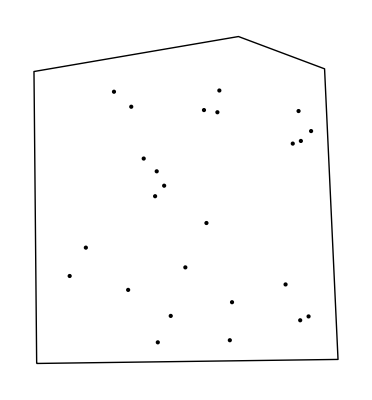

```mathematica
Show[Graphics[Point/@v], Boundary[p]]
```

```mathematica
q=VoronoiToTissue[v, p]
```

Tissue[{{2.68394,72.9156},{14.8419,78.3253},{15.2034,2.4841},{21.0852,60.9636},{21.8364,30.3927},{33.8627,64.8305},{34.4246,42.9938},{36.5999,14.5834},{37.4756,42.1157},{40.4526,64.4054},{43.7221,26.2431},{46.1335,114.335},{46.374,85.9082},{47.1463,46.2246},{47.3693,107.624},{50.0568,81.3291},{51.6204,54.7956},{56.4303,4.87285},{58.2919,21.859},{59.3328,74.1697},{59.8396,73.9028},{60.0977,13.7843},{63.3014,95.1015},{65.1087,70.083},{68.788,35.9301},{72.6457,69.3379},{75.7113,38.1667},{80.2136,93.5798},{80.3007,87.749},{82.1092,12.5129},{83.048,16.0545},{87.4338,53.2662},{92.792,85.5227},{94.5169,20.7378},{94.587,85.6616},{103.56,52.4425},{110,-1},{105,107},{73,119},{-3,106},{-2,-2.5},{108.527,30.8128},{107.545,52.0172},{106.562,73.2699},{105.667,92.6016},{85.5809,114.282},{46.1327,114.404},{-2.70404,73.8879},{-2.43073,44.2338},{11.5886,-2.31801},{56.6231,-1.71487},{86.0317,-1.321},{104.561,-1.07284}},{{1,2},{1,4},{1,48},{2,12},{2,13},{3,5},{3,8},{3,50},{4,6},{4,7},{5,7},{5,49},{6,10},{6,16},{7,9},{8,11},{8,18},{9,11},{9,14},{10,17},{10,20},{11,19},{12,15},{12,47},{13,15},{13,16},{14,17},{14,25},{15,23},{16,20},{17,24},{18,22},{18,51},{19,22},{19,25},{20,21},{21,23},{21,24},{22,30},{23,28},{24,26},{25,27},{26,29},{26,32},{27,31},{27,32},{28,29},{28,46},{29,33},{30,31},{30,52},{31,34},{32,36},{33,35},{33,36},{34,42},{34,53},{35,44},{35,45},{36,43},{37,42},{37,53},{38,45},{38,46},{39,46},{39,47},{40,47},{40,48},{41,49},{41,50},{42,43},{43,44},{44,45},{48,49},{50,51},{51,52},{52,53}},{{20,31,38,36,21},{18,22,35,28,19},{64,48,47,49,54,59,63},{44,53,55,49,43},{10,15,19,27,20,13,9},{35,34,39,50,45,42},{75,33,17,7,8},{66,24,23,29,40,48,65},{56,57,62,61},{11,6,7,16,18,15},{73,59,58},{13,21,30,14},{74,12,11,10,2,3},{26,30,36,37,29,25},{68,3,1,4,24,67},{37,38,41,43,47,40},{77,57,52,50,51},{76,51,39,32,33},{5,25,23,4},{16,17,32,34,22},{2,9,14,26,5,1},{27,28,42,46,44,41,31},{70,8,6,12,69},{72,58,54,55,60},{71,60,53,46,45,52,56}}]

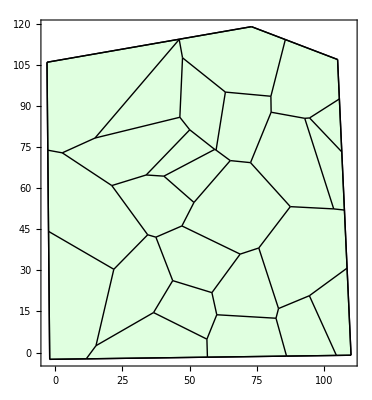

```mathematica
ShowTissue[q, Frame->True]
```